### Graphics funtions

```mathematica
ClearAll[vl,vo,polytope,cg,Vg,R,δlac,mE,y, λ,Nf, Nr,vatpMinGlobal,vatpMaxGlobal,vatpMinLocal,vatpMaxLocal,vgMinGlobal,vgMaxGlobal,vgMinLocal,vgMaxLocal,vgDistribution,vatpDistribution,totalIntegral,normalizedDistribution,distributionOfCells,showPolytope,showDensityMap, showDensityMaps, showVgDistribution, showVatpDistribution,s,showSubstrateConcentration,w,showWasteConcentration,
showCellDensity, showDilutionRate];
```

```mathematica
(* Polytope Ghaphics  -------------------------------------------------------------------------------------------------------------- *)
Module[{ vertexes, range, style, labels},

(* Layout *)
vertexes[ξ_]:=If[vatpMaxGlobal[ξ]>Nr * R,
{{vgMinGlobal,vatpMinGlobal},{Nf*vgMaxGlobal[ξ],vgMaxGlobal[ξ]},{vatpMaxGlobal[ξ],vgMaxGlobal[ξ]},{(1 + Nr)R,R/Nf}},
{{vgMinGlobal,vatpMinGlobal},{Nf*vgMaxGlobal[ξ],vgMaxGlobal[ξ]},{vatpMaxGlobal[ξ],vgMaxGlobal[ξ]}}];
range[ξ_] := PlotRange->{{-0.2vatpMaxGlobal[ξ],1.2vatpMaxGlobal[ξ]},{-0.2vgMaxGlobal[ξ],1.2vgMaxGlobal[ξ]}};
style = PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]];
labels = FrameLabel->{"v_atp (mmol/h/gDW)","v_glc (mmol/h/gDW)"};


(* Show a graph of the polytope *)
showPolytope[ξ_] := Module[{},
Print[Style["Polytope with ξ = ",25],Style[ξ,25]];
Show[
(* Plot vertexes *)
ListPlot[vertexes[ξ],style,range[ξ], labels,Frame->True,Axes->False],
(* Polytope region *)
RegionPlot[polytope[ξ][vg,vatp],{vatp,0,vatpMaxGlobal[ξ]},{vg,0,vgMaxGlobal[ξ]}]
]
];


(* Show polytope and the probability density map *)
showDensityMap[ξ_, β_ ]:= Module [{},
Show[
(* Plot vertexes *)
ListPlot[vertexes[ξ],style,range[ξ], labels,Frame->True,Axes->False,AspectRatio->1],
(* Density *)
DensityPlot[distributionOfCells[ξ, β, vatp],{vatp, vatpMinGlobal, vatpMaxGlobal[ξ] },{vg,vgMinGlobal, vgMaxGlobal[ξ]},RegionFunction-> Function[{ vatp, vg, z}, 0≤vg≤vgMaxGlobal[ξ]∧vl[vg,vatp]≤0∧0≤vo[vg,vatp]≤R], PlotRange-> All, BoundaryStyle -> Black]
]
];

];

(* Variant β value ghrapics ------------------------------------------------------------------------------------------------------- *)
Module[{βlist, plotLegend,linePoints},
βlist={0.0001,1.99 100,1.99 1000};
linePoints= Table[i ^3,{i,.01, 6,0.1}];

(* Show density maps with variable βs *)
showDensityMaps[ξ_] := Module[{ map},
Print[Style["Probability Density Maps",25]];
Print["ξ value: ",ξ];
Print["β values: ", βlist];
Table[showDensityMap[2,β],{β, βlist}]
];


showNormalizedDistribution[ξ_] := Module[{vatp,funList},
funList = Table[normalizedDistribution[ξ,β,vatp,totalIntegral[ξ,β]],{β,βlist}];
Print[Style["Normalized Probability Density Function",25]];
Print["ξ value: ", ξ];
Print[   "Total Integral Test -> ",∫_vatpMinGlobal^vatpMaxGlobal[ξ] (∫_vgMinLocal[vatp]^(vgMaxLocal[ξ][vatp]) funListⅆvg)ⅆvatp];
Plot[funList,{vatp,vatpMinGlobal,vatpMaxGlobal[ξ]},PlotRange->{All,{0,30}},AxesLabel->{"vatp", "normalized probability density"}, PlotLegends-> Table[StringJoin["β: ",ToString[β]],{β,βlist}]]
];

showVatpDistribution[ξ_] := Module[{funList, integralsList,vatp},
funList = Table[vatpDistribution[ξ,β,vatp,totalIntegral[ξ,β]],{β,βlist}];
Print[Style["Propbability Density of Vatp",25]];
Print["ξ value: ", ξ];
Print[   "Total Integral Test -> ",∫_vatpMinGlobal^vatpMaxGlobal[ξ] funListⅆvatp];
Plot[funList, {vatp,vatpMinGlobal,vatpMaxLocal[ξ]},PlotRange->{All,{0,15}},AxesLabel->{"vatp", "probability density"}, 
PlotLegends-> Table[StringJoin["β: ",ToString[β]],{β,βlist}]]
];

showVgDistribution[ξ_] := Module[{vg,funList},
funList = Table[vgDistribution[ξ,β,vg,totalIntegral[ξ,β]],{β,βlist}];
Print[Style["Propbability Density of Vg",25]];
Print[   "Total Integral Test -> ",∫_vgMinGlobal^vgMaxGlobal[ξ] funListⅆvg];
Plot[funList, {vg,vgMinGlobal,vgMaxGlobal[ξ]},PlotRange->{All,{0,15}}, AxesLabel->{"vg", "probability density"},
 PlotLegends-> Table[StringJoin["β: ",ToString[β]],{β,βlist}]
]
];


showSubstrateConcentration := Module[{listToGraph},
listToGraph = Table[Table[s[ξ,β],{ξ,linePoints}],{β,βlist}];
Print[Style["Substrate Concentration",25]];
ListLogLinearPlot[listToGraph, Joined -> True, PlotRange->All, PlotLegends-> Table[StringJoin["β: ",ToString[β]],{β,βlist}],AxesLabel->{"ξ", "sg"}]
];


showWasteConcentration := Module[{listToGraph},
listToGraph = Table[Table[w[ξ,β],{ξ,linePoints}],{β,βlist}];
Print[Style["Waste Concentration",25]];
ListLogLinearPlot[listToGraph, Joined -> True, PlotRange->All, PlotLegends-> Table[StringJoin["β: ",ToString[β]],{β,βlist}],
AxesLabel->{"ξ", "sl"}]
];

showDilutionRate :=  Module[{listToGraph},
listToGraph = Table[Table[d[ξ,β],{ξ,linePoints}],{β,βlist}];
Print[Style["Dilution Rate",25]];
ListLogLinearPlot[listToGraph, Joined -> True, PlotRange->{{10,All},{0, All}}, PlotLegends-> Table[StringJoin["β: ",ToString[β]],{β,βlist}],
AxesLabel->{"ξ", "D"}]
];

showCellDensity :=  Module[{listToGraph},
listToGraph = Table[Table[x[ξ,β],{ξ,linePoints}],{β,βlist}];
Print[Style["Cell Density",25]];
ListLogLinearPlot[listToGraph, Joined -> True,PlotRange->{{10,All},{0, All}}, PlotLegends-> Table[StringJoin["β: ",ToString[β]],{β,βlist}],
AxesLabel->{"ξ", "X"}]
];
]
```

# Toy Model

## Introduction

------ Parameters ------

cg (Millimolar)-> glc in feed.
Vg(Millimoles/Grams/Hours) → max glc uptake.
R (Millimoles/Grams/Hours) → max uptake of pyruvate by mitochondria (max.respiration).
mE(Millimoles/Grams/Hours) → maintenance ATP demand.
δlac(Millimolar/Hours) → lac death rate.
y(Millimoles/Grams)→ units of metabolite needed per unit of biomass produced.

### Values

```mathematica
cg = 15;
Vg = 0.5;
R = 0.4;
δlac = 0.0022/2;
mE = 1;
y = QuantityMagnitude[1/UnitConvert[Quantity[0.24393939393939396,"Moles"/"Grams"],"Millimoles"/"Grams"]];
Nf = 2;
Nr = 19;
ϕ = 1;
{cg,Vg,R,y,δlac,mE}=Rationalize[{cg,Vg,R,y,δlac,mE}];
```

------ Functions ------

### Balance equations and Constrains

Balance equation for P
Nf*vg + vl - vo = 0 →(6)

Balance equation  for ATP
Nf*vg + Nr*vo  = vapt  → (7)

Constraint of vg
vg ≤ min{Vg, cg * D/X}  → (8)

Constraint of vl
vl ≤ 0 → (9)

Contraint of vo
0 ≤ vo ≤ R → (9)

Taking the upper bound of vg you get Mg (The maximum glucose uptake)
Mg = min{Vg, cg *ξ}

### Growth function

Rate of biomass synthesis
We consider the ATP requirement of growth and maintinance and ingnore additional biomass components
z = (vatp - mE) * y 

Death rate
We assume that the secreted lactate is toxic, so the death will depend of its concentration in the culture (sl)
δ = δlac * sl 

Net growth rate
λ = z - δ 

Maximum net growth rate
The growth rate is maximum when vatp is maximum too
λmax = z[vatpmax] - δ → (0.5)

## Model Solution

------ Polytope (𝒫_s)------

### Definition

"The constraints and balance equations defined above define a polytope of feasible metabilic states that we denote (𝒫_s). Each point within this space, in the Toy model, consists of coordinates v = (vg,vatp), wich fully specify the metabolic state of a cell in the model. "

"The constraints and balance equations defined above define a polytope of feasible metabilic states that we denote (𝒫_s). Each point within this space, in the Toy model, consists of coordinates v = (vg,vatp), wich fully specify the metabolic state of a cell in the model. "

"To solve the model we put all the unknow variables in depende of vg and vatp (chosen for convenience)"

"Clearing vo from Eq.6 and 7"

```mathematica
vl[vg_,vatp_]:=(vatp-Nf*vg*(1+Nr))/Nr;
```

"Clearing vo from Eq.6"

```mathematica
vo[vg_,vatp_]:=(vatp-Nf*vg)/Nr;
```

"All points in the polytope most solve the constraints 0 ≤ vg ≤ Mg  &&  vl ≤ 0  && 0 ≤ vo ≤ R"

```mathematica
polytope[ξ_][vg_,vatp_]:=0≤vg≤vgMaxGlobal[ξ]∧vl[vg,vatp]≤0∧0≤vo[vg,vatp]≤R;
```

### Polytope limits

" To calculate any integral through the polytope it is useful to defind its limits... "

```mathematica
ClearAll[vo,vl,vatpMaxGlobal,vatpMaxLocal,vatpMinGlobal,vatpMinLocal,vgMaxGlobal,vgMaxLocal,vgMinGlobal,vgMinLocal]
vo[vg_,vatp_]:=(vatp-Nf*vg)/Nr;
vl[vg_,vatp_]:=(vatp-Nf*vg*(1+Nr))/Nr;

vgMinGlobal = 0;
vgMaxGlobal[ξ_] :=   Min[Vg,cg/ξ];
vgMinLocal[vatp_]:=Max[vatp/(1+Nr),vatp-Nr*R]/Nf;
vgMaxLocal[ξ_][vatp_]:=Min[vgMaxGlobal[ξ],vatp/Nf];

vatpMinGlobal = vatpMinLocal[vgMinGlobal];
vatpMaxGlobal[ξ_]:=vatpMaxLocal[vgMaxGlobal[ξ]];
vatpMinLocal [vg_] := Nf*vg; 
vatpMaxLocal[vg_] := Min[Nf(1+Nr)vg,Nf*vg+Nr*R];

polytope[ξ_][vg_,vatp_]:=vgMinLocal[vatp]≤vg≤vgMaxLocal[ξ][vatp]∧vatpMinLocal[vg] ≤ vatp ≤ vatpMaxLocal[vg];
```

Polytope with ξ = 2

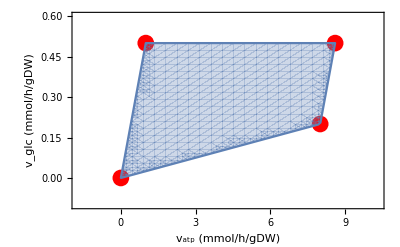

```mathematica
showPolytope[2]
```

------ Probability Distribution------

### Maximum Entropy and Probabolity Distribution

" Let P(v) be the probabilistic density of cells with metabolic fluxes v. To determine the form of P(v)dv, we adopt the Princile of Maximum Entropy (MaxEnt), which in this context can be  stated as follows:"

" Given the set of allowed metabolic states (𝒫_s), the dependency of the cellular growth rate with metabolic fluxes (λ_s(v)), and the average growth rate of the cell population ⟨λ⟩, the distribution of cells within 𝒫_s has the form ⅇ^(β*λ[v]),"

```mathematica
distributionOfCells[ξ_,β_,vatp_] := Exp[-β y(vatpMaxGlobal[ξ]-vatp)];
```

"where β is chosen so that the expectation of λ under (𝒫_s) coincides with ⟨λ⟩."

Probability Density Maps

ξ value: 2

β values: {0.0001,199.,1990.}

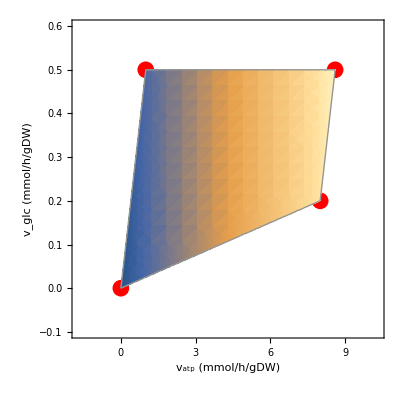
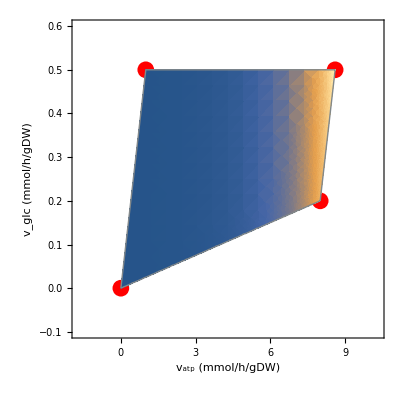
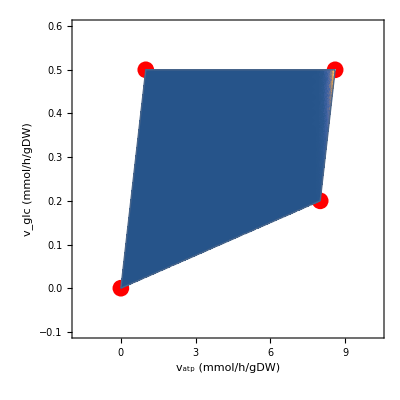

```mathematica
showDensityMaps[2]
```

### Normalized Distribution

"So, the normalized distribution can be defined"

```mathematica
normalizedDistribution[ξ_,β_,vatp_,totalIntegral_] := distributionOfCells[ξ,β,vatp]/totalIntegral;
```

" where totalIntegral is the value of the integral in the whole polytope, "

```mathematica
totalIntegral[ξ_,β_] := ∫_vatpMinGlobal^vatpMaxGlobal[ξ] (∫_vgMinLocal[vatp]^(vgMaxLocal[ξ][vatp]) distributionOfCells[ξ,β,vatp]ⅆvg)ⅆvatp ;
```

Normalized Probability Density Function

ξ value: 2

Total Integral Test -> {1.,1.,1.}

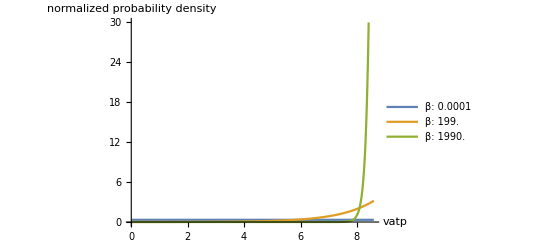

```mathematica
showNormalizedDistribution[2]
```

### Probability associated to vatp

" So, the probability of vatp in the population of cells can be calculated: “

```mathematica
vatpDistribution[ξ_,β_,vatp_,totalIntegral_] := ∫_vgMinLocal[vatp]^(vgMaxLocal[ξ][vatp]) normalizedDistribution[ξ,β,vatp,totalIntegral]ⅆvg;
```

Propbability Density of Vatp

ξ value: 2

Total Integral Test -> {1.,1.,1.}

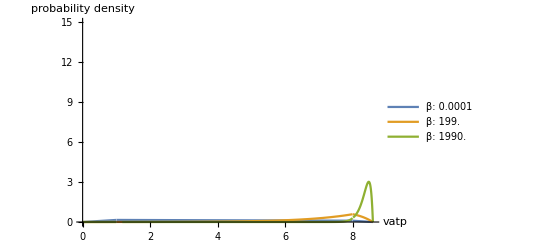

```mathematica
showVatpDistribution[2]
```

### Probability associated to vg

" Also, the probability of vg is calculated as: “

```mathematica
vgDistribution[ξ_,β_,vg_,totalIntegral_] := ∫_vatpMinLocal[vg]^vatpMaxLocal[vg] normalizedDistribution[ξ,β,vatp,totalIntegral]ⅆvatp;
```

Propbability Density of Vg

Total Integral Test -> {1.,1.,1.}

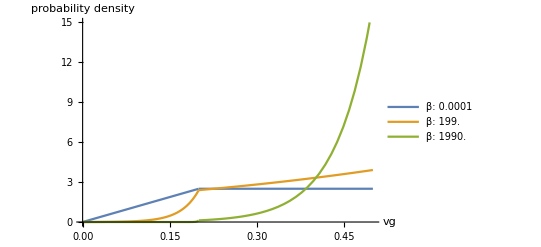

```mathematica
showVgDistribution[2]
```

## Results

"In this toy model, the total consumption of glucose of the population of cells can be estimated“

```mathematica
expectedVg[ξ_,β_] := ∫_vatpMinGlobal^vatpMaxGlobal[ξ] (∫_vgMinLocal[vatp]^(vgMaxLocal[ξ][vatp]) normalizedDistribution[ξ,β,vatp, totalIntegral[ξ,β]]vgⅆvg)ⅆvatp;
```

"Next, the value of the glucose concentration are obtained from...“

```mathematica
s[ξ_,β_] :=Max[0, cg - expectedVg[ξ,β]ξ];
```

"The expected waste uptake are given by..."

Substrate Concentration

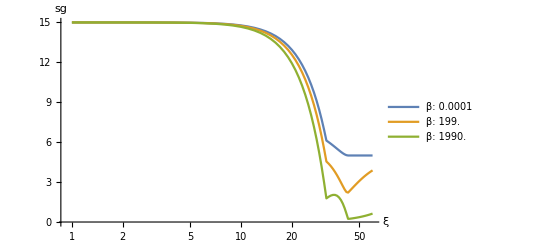

```mathematica
showSubstrateConcentration
```

```mathematica
expectedVw[ξ_,β_] := ∫_vatpMinGlobal^vatpMaxGlobal[ξ] (∫_vgMinLocal[vatp]^(vgMaxLocal[ξ][vatp]) normalizedDistribution[ξ,β,vatp, totalIntegral[ξ,β]]((vatp -38 expectedVg[ξ,β])/18)ⅆvg)ⅆvatp//N;
```

"The same way, we can calculated the waste concentration in the medium...“

```mathematica
w[ξ_,β_] :=Max[0, - expectedVw[ξ,β]*ξ];
```

Waste Concentration

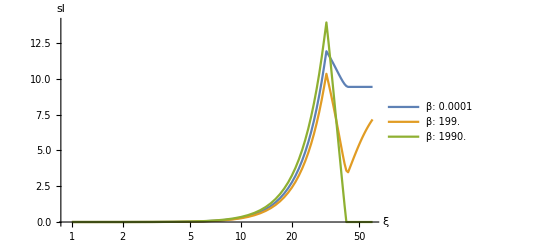

```mathematica
showWasteConcentration
```

```mathematica
expectedZ[ξ_, β_] := ∫_vatpMinGlobal^vatpMaxGlobal[ξ] (∫_vgMinLocal[vatp]^(vgMaxLocal[ξ][vatp]) ((vatp - mE)*y)ⅆvg)ⅆvatp//N;
λ[ξ_,β_] := expectedZ[ξ,β] - δlac * w[ξ,β]; 
d[ξ_,β_] := λ[ξ,β]/ϕ;
```

Dilution Rate

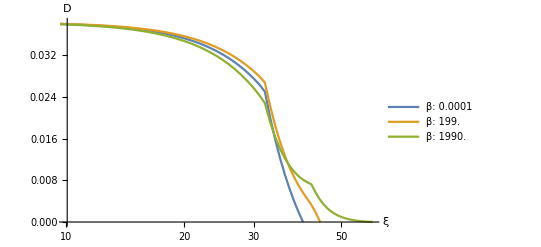

```mathematica
showDilutionRate
```

```mathematica
x[ξ_,β_] := λ[ξ,β]*ξ/ϕ;
```

Cell Density

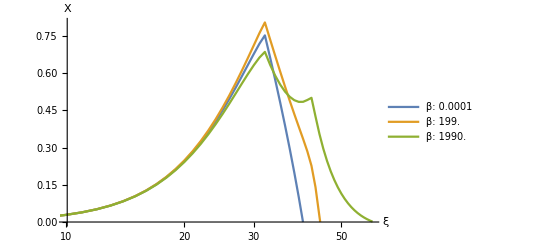

```mathematica
showCellDensity
```